```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\packages\\graph_toolbox.wl"]
```

#### Transitioning between states by updating a single rod length

a possible state {initial condition}

{0.6,1,0.6,1,0.6,0.6,0.6,0.6,0.6,1,0.6,1}

initial condition neighbours

(1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1
0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6)

First neighbours' neighbours

(0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 1 | 1
1 | 1 | 0.6 | 1 | 0.6 | 0.6 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 0.6)

A graph that shows the transition from a state to its neighbours and their neighbours in turn

-Graphics-

Plot of the end effector locations the mechanism can transition to abd the locations it could move to thereafter

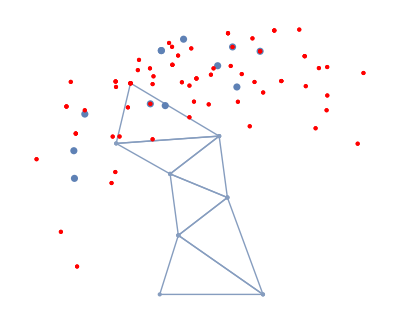

```mathematica
nrods =12;
shortlength = 0.6;
longlength = 1;

fixed1 = {0,0};
fixed2 = {1,0};

Echo["a possible state {initial condition}"];
possiblestate =  MakeState[RandomInteger[2^nrods],nrods]

Echo["initial condition neighbours"];
ns =  FindNeighbours[possiblestate];(*//MatrixForm*)
ns //MatrixForm

Echo["First neighbours' neighbours"];
nns = FindNeighbours/@ns;
nns[[1]]//MatrixForm

Echo["A graph that shows the transition from a state to its neighbours and their neighbours in turn"];
g1 =Graph[Join[StateToNeighbours[possiblestate,Green],
Flatten[Table[StateToNeighbours[ns[[i]],Red],{i,Range[nrods]}]]]]

nc = MakeTriangleWorm[fixed1,fixed2,#]&/@ns;
nnc = MakeTriangleWorm[fixed1,fixed2,#]&/@Flatten[nns,1];
ne = nc[[All,-1,All]];
nne = nnc[[All,-1,All]];

Echo["Plot of the end effector locations the mechanism can transition to abd the locations it could move to thereafter"];
g2 =Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[ne],ListPlot[nne,PlotStyle->{PointSize[Medium],Red}]]
```

#### The state transition diagram if all states can transition to all other states

```mathematica
nrods=8;
shortlength=0.6;
longlength=1;
allstates=Tuples[{shortlength,longlength},nrods];
Graph[Flatten[StateToNeighbours[#,Black]&/@allstates]]
```

-Graphics-

#### Transitioning between randomly states and their neighbours

```mathematica
nrods = 10;
shortlength = 0.6;
longlength = 1;
fixed1 = {0,0};
fixed2 = {1,0};

maxstates = 2^nrods;
chosenstates = MakeState[#,nrods]&/@RandomInteger[maxstates,100];

transitions = Tooltip[#,PlotCoordTransition[#]]&/@Flatten[StateToNeighbours[#,Black]&/@chosenstates];
Graph[transitions]
```

-Graphics-

#### Transition from random state to neighbours and then to neighbours’ neighbours a few times

```mathematica
nrods=12
nnest = 3
possiblestate =  MakeState[RandomInteger[2^nrods],nrods]
s =Rest@NestList[Flatten[Table[#->n,{n,FindNeighbours@#}]&/@#[[All,2]],1]&,{possiblestate->possiblestate},nnest];
Graph[Flatten[s]]
```

12

3

{0.6,0.6,0.6,1,0.6,1,0.6,0.6,0.6,1,1,0.6}

-Graphics-

#### Show the actual transitioning between states

```mathematica
nrods =6;
shortlength = 0.6;
longlength = 1;
fixed1 = {0,0};
fixed2 = {1,0};

maxstates = 2^nrods;

chosenstates = MakeState[#,nrods]&/@RandomInteger[maxstates,10];
transitions =Flatten[StateToNeighbours[#,Black]&/@chosenstates];
```

```mathematica
ef1[el_,___]:=Arrow[el,0.25];
Graph[transitions,EdgeStyle->Dashed, EdgeShapeFunction->ef1, VertexShapeFunction->(Inset[Framed@MeshColorAllTriag[MakeTriangleWorm[fixed1,fixed2,#2],{{0,2},{-0.1,1.5}}],#1,Center,0.4]&),GraphLayout->Automatic]
```

-Graphics-

#### Shortest path between states

```mathematica
nrods = 10;
shortlength = 0.6;
longlength = 1;
fixed1 = {0,0};
fixed2 = {1,0};

maxstates = 2^nrods;
chosenstates = MakeState[#,nrods]&/@RandomInteger[maxstates,1000];

transitions =Flatten[StateToNeighbours[#,Automatic]&/@chosenstates];
g =Graph[transitions]
```

```mathematica
startstate := RandomChoice[chosenstates];
endstate := RandomChoice[chosenstates];
shortpath =FindShortestPath[g,startstate,endstate];
```

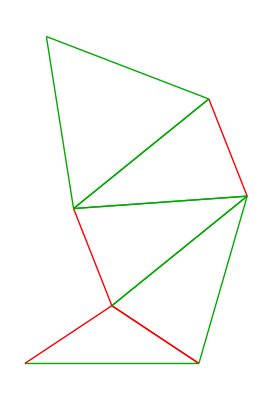
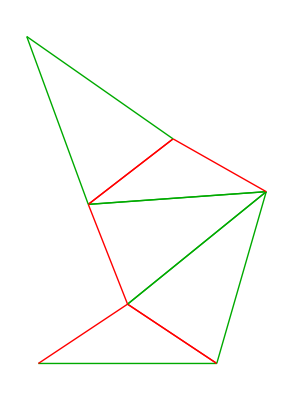
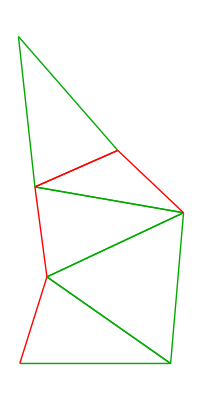
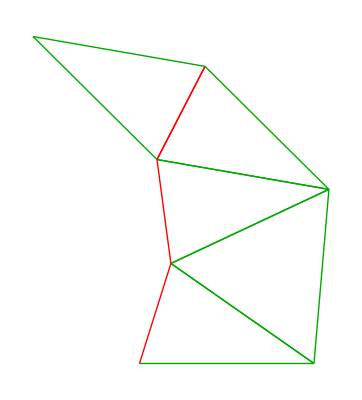
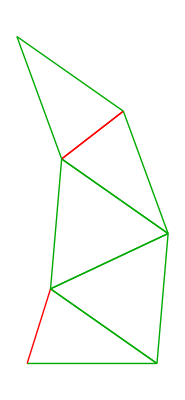
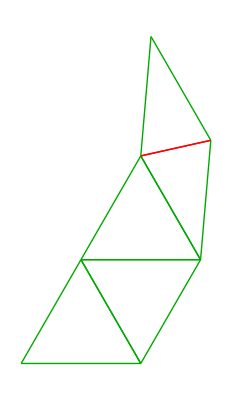
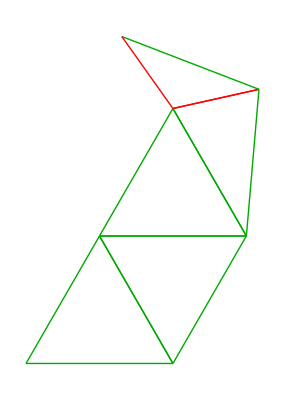
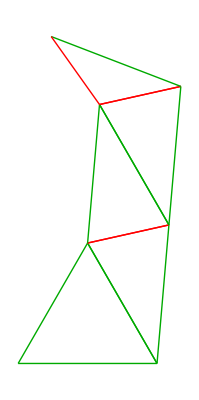

```mathematica
MeshColorAllTriag[MakeTriangleWorm[fixed1,fixed2,#],All]&/@shortpath
```

If you are fine with this jagged motion you can as well change all states simultaneously

#### smoothest path transition between states

```mathematica
shortestallowablepath=2;
longestallowablepath = 10;
npathstofind=100;
pathsbetween=FindPath[g,startstate,endstate,{shortestallowablepath,longestallowablepath},npathstofind];
```

```mathematica
apathbetween=pathsbetween[[1]];
```

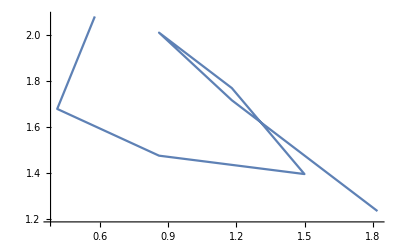

0.0796021

```mathematica
ListLinePlot[AllCoordsForStatePath[apathbetween]]
SmallCoordChangeMetric[apathbetween]
```

```mathematica
metrics =SmallCoordChangeMetric/@pathsbetween;
optpathloc =Min[Position[metrics,Min[metrics]]];
Echo[metrics[[optpathloc]]];
```

0.0691241

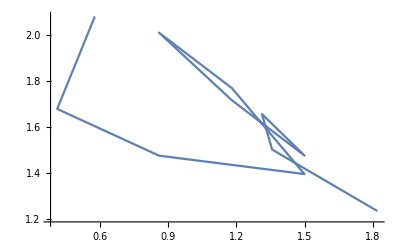

```mathematica
ac= AllCoordsForStatePath[pathsbetween[[optpathloc]]];
ListLinePlot[ac]
```